# Някои практически въпроси, свързани с интерполацията. Приложения.

Задача 1: Да се напише функция newtonPoly[nodes_,values_,x_], която връща в нормален вид полинома на Нютон p(x) за възлите nodes и стойности values.

Задача 2: В таблицата са дадени данни за населението на САЩ в периода 1920-1990. Да се построи полином от седма степен, интерполиращ таблицата.
 Да се даде приближение на населението през 1952, 1974, 2000 година и да се сравни с действителните стойности - съответно
 157млн, 214 млн, 281.42млн.
 
 година | 1920 | 1930 | 1940 | 1950 | 1960 | 1970 | 1980 | 1990
население | 106.46 | 123.08 | 132.12 | 152.27 | 180.67 | 205.05 | 227.23 | 249.46

Задача 3: Да се приближи функцията f(x)=1/(1+25 x^2) в интервала [-1;1], като се намерят интерполационните полиноми от степени 10 и 4 при рваноотдалечеи възли.
Да се построят графиките на абсолютните грешки в двата случая.

Задача 4: Да се състави анимация по зададените сцени:

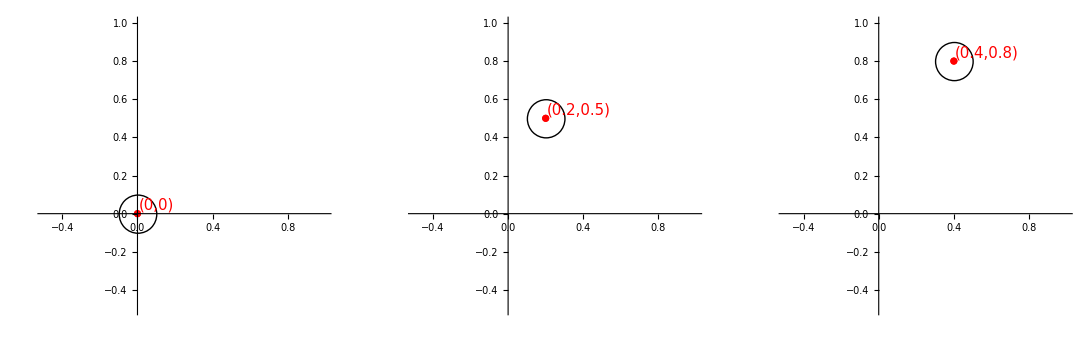

За целта използвайте следния код, като на маркираните в жълто полета заместите правилните стойности:

```mathematica
Animate[Graphics[Circle[{x_coordinate_of_center,y_coordinate_of_center},0.1],Axes->True,
AxesOrigin->{0,0}, PlotRange->{{-0.5,1},{-0.5,1}}],{x,0,0.4,0.01}]
```

Задача 5: Проведени са експерименти, за да се определи бързодействието на един алгоритъм за сортиране в зависимост от броя елементи. Резултатите са представени в следната таблица:
 бр. е/ти, хил | 10 | 20 | 50 | 100 | 150 | 200 | 250
време, s | 0.1639275 | 0.53282 | 3.00007 | 11.20784 | 26.7486723 | 47.3297 | 76.80605
Да се определи колко най-много елемента могат да се сортират за не повече от 30сек.

```mathematica
(*Functions for finding interpolation polynomials with using newtons formula*)
dividedDiff[nodes_,vals_]:=(If[Length[nodes]==1,vals[[1]],((dividedDiff[nodes[[2;;Length[nodes]]],vals[[2;;Length[nodes]]]]-dividedDiff[nodes[[1;;Length[nodes]-1]],vals[[1;;Length[nodes]-1]]])/(nodes[[Length[nodes]]]-nodes[[1]]))]);
 newtonPoly[nodes_, values_, x_] := (values[[1]]+Sum[dividedDiff[nodes[[1;;n]], values[[1;;n]]]*Product[x-nodes[[i]],{i,1,n-1}], {n, 2, Length[nodes]}]);
```

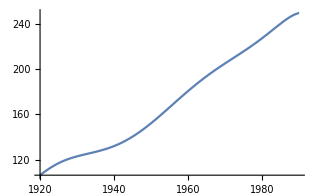
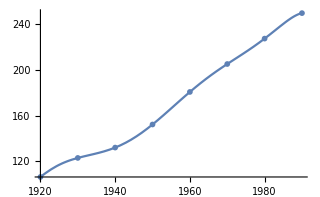
```mathematica
(*Exercise 2*)
values = {106.46,123.08,132.12,152.27,180.67,205.05,227.23,249.46};
nodes = {1920,1930,1940,1950,1960,1970,1980,1990};
f[x_]:= newtonPoly[nodes,values,x];
f[x]
106.46+1.6620000000000006 (-1920+x)-0.037899999999999996 (-1930+x) (-1920+x)+0.0031149999999999993 (-1940+x) (-1930+x) (-1920+x)-0.00008979166666666674 (-1950+x) (-1940+x) (-1930+x) (-1920+x)+1.0116666666666757*^-6 (-1960+x) (-1950+x) (-1940+x) (-1930+x) (-1920+x)+1.577777777777729*^-8 (-1970+x) (-1960+x) (-1950+x) (-1940+x) (-1930+x) (-1920+x)-9.626984126983942*^-10 (-1980+x) (-1970+x) (-1960+x) (-1950+x) (-1940+x) (-1930+x) (-1920+x)

plotOne = Plot[f[x], {x, 1920, 1990}];
Show[plotOne]
-Graphics-
f[2000]
175.08000000000197
plotTest2 =  ListPlot[{{1920, 106.46}, {1930, 123.08},{1940, 132.12},{1950,152.27},{1960,180.67},{1970,205.05},{1980,227.23},{1990,249.46}}];
Show[{plotOne, plotTest2}]
-Graphics-
```

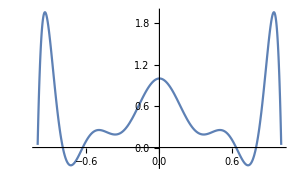
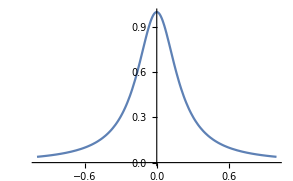
```mathematica
(*Exercise 4*)
g[x_]:= 1/(1+25*x^2);

funcNodes = {-1,-0.8,-0.6, -0.4, -0.2,0, 0.2 ,0.4,0.6, 0.8,1};
funcVal = g[funcNodes];

poly = newtonPoly[funcNodes,funcVal,x];

poly//Simplify
Plot[newtonPoly[funcNodes,funcVal,x],{x,-1,1}]

1.-4.440892098500626*^-16 x-16.855203619909506 x^2+3.552713678800501*^-15 x^3+123.35972850678732 x^4-7.638334409421077*^-14 x^5-381.4338235294118 x^6+494.9095022624435 x^8-220.94174208144796 x^10

(*The graph is so squigly because we are using a high-degree polynomial and all of the arithmetic errors add up.*)
-Graphics-
Plot[g[x],{x,-1,1}]
-Graphics-
```

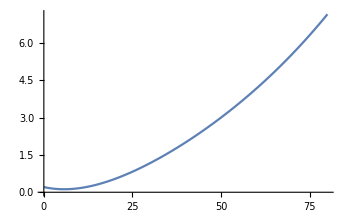
```mathematica
(*Exercise 5*)
numberOfElements = {10,20,50,100,150,200,250};
{{0.1639275,0.53282,3.00007,11.20784,26.7486723,47.3297,76.80605}}
secondsForNumberOfelements = {0.1639275,0.53282,3.00007,11.20784,26.7486723,47.3297,76.80605};
sortingPoly[x_] := newtonPoly[ numberOfElements,secondsForNumberOfelements, x];
sortingPoly[x]//Simplify
Plot[sortingPoly[x], {x, 0, 80}]

0.20863216258909525-0.03201288576171462 x+0.0031765882206562634 x^2-0.00004655860654061431 x^3+4.5113240716038647*^-7 x^4-1.902494984405294*^-9 x^5+2.9049298756483345*^-12 x^6
-Graphics-

Solve[sortingPoly[x] == 30, x]
{{x->-59.23867688971319},{x->19.034245575406935-118.90448625932092 ⅈ},{x->19.034245575406935+118.90448625932092 ⅈ},{x->158.46399028254143},{x->258.8128068856482-91.41826130049292 ⅈ},{x->258.8128068856482+91.41826130049292 ⅈ}}
x->158.46399028254143 (*Number of elements that can be sorted for up to 30seconds (in thousands)*)
```